```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_surface"];
filesMesh={"1.xye0" ,"2.xye0", "3.xye0" ,"4.xye0" ,"5.xye0" ,"6.xye0","7.xye0" ,"8.xye0", "9.xye0","10.xye0" ,"11.xye0"};
meshData=Table[ReadList[filesMesh[[i]],{Number, Number,Number}],{i,1,11}];
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_surface/retouched"];
filesMeshr={"1.xye0" ,"2.xye0", "3.xye0" ,"4.xye0" ,"5.xye0" ,"6.xye0","7.xye0" ,"8.xye0", "9.xye0","10.xye0" ,"11.xye0"};
meshDatar=Table[ReadList[filesMesh[[i]],{Number, Number,Number}],{i,1,11}];
```

```mathematica
meshData[[1]];
```

```mathematica
Sqrt[meshData[[1]][[10]][[1]]^2+meshData[[1]][[10]][[2]]^2]
```

0.225

```mathematica
Transpose[meshData[[1]]][[3]]
```

{51.2866,63.2032,101.117,90.8264,67.2782,42.9245,25.7322,15.2429,10.3982,10.6136,1993.93,15.287,22.4749,26.2228,49.3085,45.2586,35.7916,25.7322,17.2169,11.5811,9.43402,1142.71,9.96397,12.2451,15.3381,16.8675,25.4208,23.698,19.6935,15.2429,11.5811,10.0349,421.246,11.1364,14.3004,18.364,22.2348,23.8808,17.9766,16.3577,13.0897,10.3982,9.43402,147.334,11.1364,16.2544,24.2881,34.1628,43.5451,47.5739,26.918,23.0797,15.6677,10.6136,61.5044,9.96397,14.3004,24.2881,41.2598,65.3307,89.0027,99.5801,63.7501,51.6438,29.4493,26.0382,15.287,12.2451,18.364,34.1628,65.3307,112.786,176.251,212.197,127.29,99.5169,11.8085,51.2866,22.4749,15.3381,22.2348,43.5451,89.0027,176.251,327.724,421.247,165.127,5.16715,126.939,63.2032,26.2228,16.8675,23.8808,47.5739,99.5801,212.197,421.247,557.307,2.03306,1994.9,1143.34,422.596,150.51,65.3512,31.4557,24.1645,44.8343,127.333,325.958,0.72572,1993.93,587.684,1143.34,772.72,328.928,129.937,59.2557,29.0846,21.4958,37.2207,99.7761}

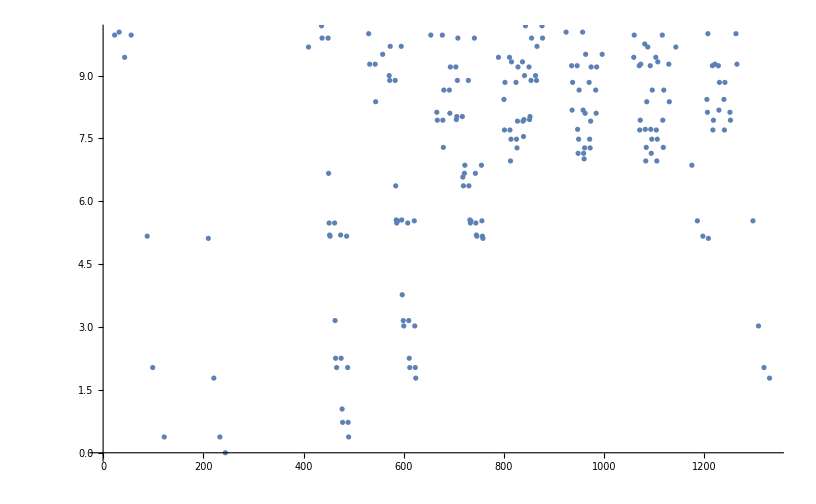

```mathematica
ListPlot[Flatten@Table[Transpose[meshDatar[[i]]][[3]],{i,1,11}],PlotRange->{All,{0,10}}]
```

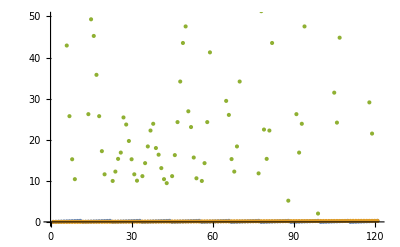

```mathematica
ListPlot[Transpose[meshDatar[[1]]],PlotRange->{All,{0,50}}]
```

```mathematica
mod[data_]:=Sqrt[data[[1]]^2+data[[2]]^2]
mod2[data_]:=Sqrt[data[[1]]^2+data[[2]]^2]-0.21
f[data_]:=If[0≥mod[data]≥0.04||0≥(mod2[data])≥0.04,data, {data[[1]],data[[2]],1000}]
mod[meshData[[1]][[30]]]
newData=Table[f[meshData[[1]][[i]]],{i,1,50}];
newData//TableForm;
```

0.1820027472320129568

```mathematica
ListContourPlot[newData,InterpolationOrder->1,PlotLegends->Automatic,PlotRange->{0,150}]
```

-Graphics-

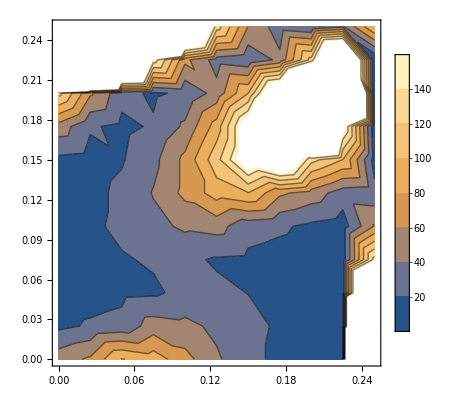

```mathematica
Show@Table[ListContourPlot[meshData[[i]],InterpolationOrder->1,PlotLegends->Automatic,PlotRange->{0,150}],{i,1,1}]
```

```mathematica
ListPlot3D[meshDatar[[1]],PlotRange->{-1,100},AxesLabel->{"a","b","Energy"}]
```

-Graphics3D-

```mathematica
GraphicsGrid[{Table[ListPlot3D[meshDatar[[i]],PlotRange->{-1,100},AxesLabel->{"a","b","Energy"}],{i,1,11}]},ImageSize->3000]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListPlot3D[meshDatar[[i]],PlotRange->{-1,50},AxesLabel->{"a","b","Energy"}],{i,1,11}]},ImageSize->3000]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListPlot3D[meshDatar[[i]],PlotRange->{-1,12},AxesLabel->{"a","b","Energy"}],{i,1,11}]},ImageSize->3000]
```

-Graphics-

```mathematica
ListPlot3D[meshData[[1]],PlotRange->{-10,100},AxesLabel->{"a","b","Energy"}]
```

-Graphics3D-

```mathematica
ListPlot3D[meshData[[10]],InterpolationOrder->6,PlotLegends->Automatic,PlotRange->{0,1}]
```

-Graphics3D-

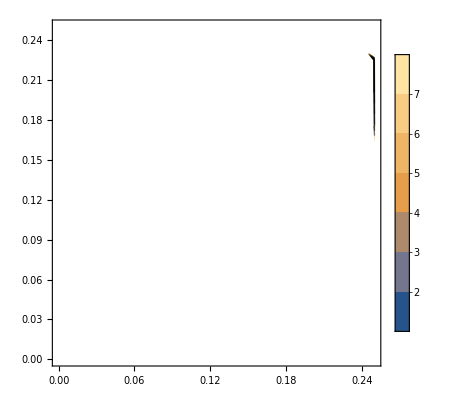
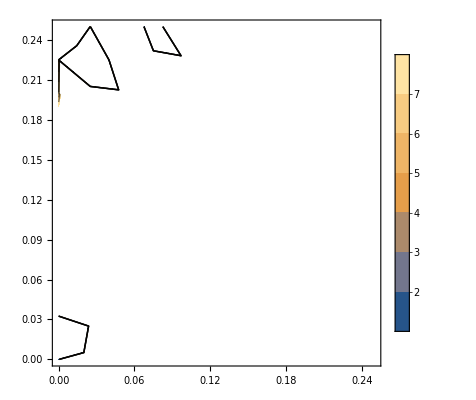
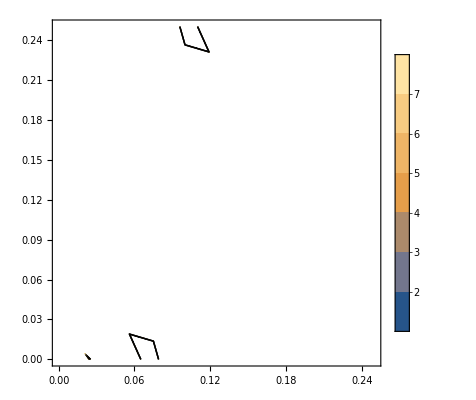
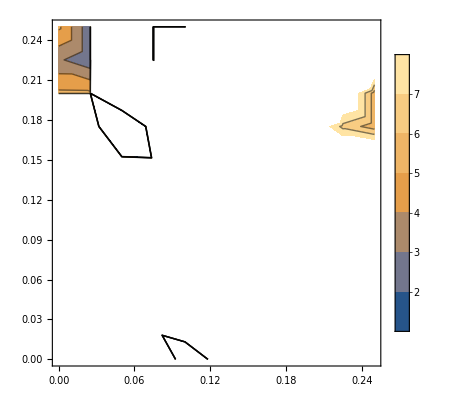
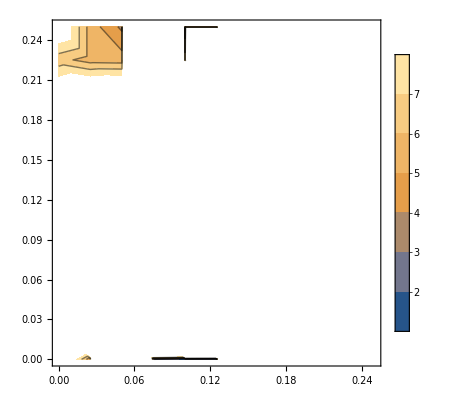
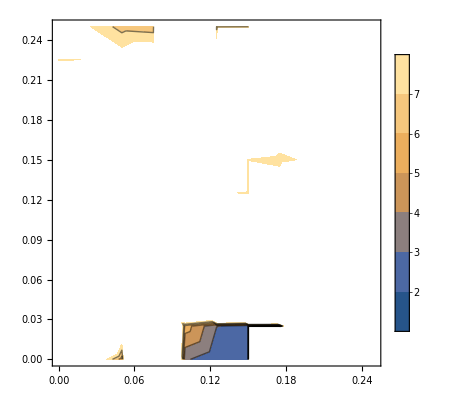
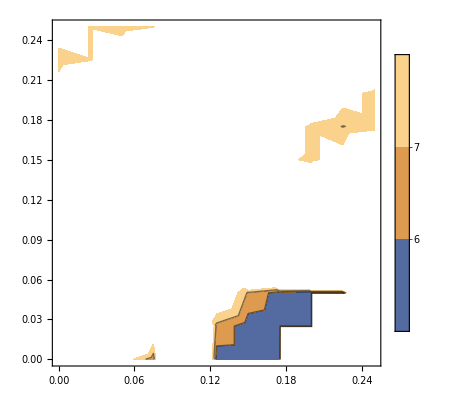
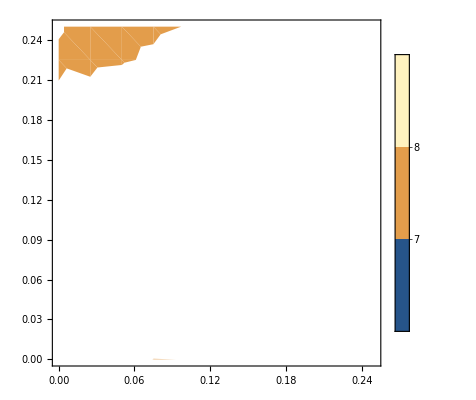

```mathematica
Table[ListContourPlot[meshData[[i]],InterpolationOrder->1,PlotLegends->Automatic,PlotRange->{1,8}],{i,1,11}]
```

```mathematica
1
```